```mathematica
expo=(v^2/3-(v-Subscript[μ, q])^2/2)//Expand
```

-v^2/6+v μ_q-μ_q^2/2

```mathematica
D[expo,v]
```

-v/3+μ_q

```mathematica
expo/.{v->3 Subscript[μ, q]}
```

μ_q^2

```mathematica
effsq1=(9 √3 ⅇ^(v^2/3-1/2 (v-Subscript[μ, q])^2) (186 √5+240 √5 Subscript[μ, q]^2+25 (-5+3 √5) Subscript[μ, q]^4))/(125 (12+v^2) Subscript[μ, q]^2)
```

(9 √3 ⅇ^(v^2/3-1/2 (v-μ_q)^2) (186 √5+240 √5 μ_q^2+25 (-5+3 √5) μ_q^4))/(125 (12+v^2) μ_q^2)

```mathematica
e1=effsq1/.{v->3 Subscript[μ, q]}
```

(9 √3 ⅇ^(μ_q^2) (186 √5+240 √5 μ_q^2+25 (-5+3 √5) μ_q^4))/(125 μ_q^2 (12+9 μ_q^2))

```mathematica
Minimize[{e1,Subscript[μ, q]>0.},{Subscript[μ, q]}]
```

{15.7628,{μ_q→0.904764}}

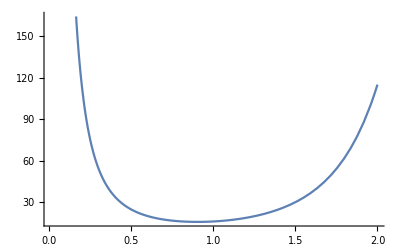

```mathematica
Plot[e1,{Subscript[μ, q],0.01,2.}]
```

```mathematica
FindMinimum[e1,{Subscript[μ, q],0.8}]
```

{15.7628,{μ_q→0.904764}}

```mathematica
effsq1gwd1=(9 √3 ⅇ^(Subscript[μ, q]^2/3) (1+2/κ^2) (-(κ^2 Subscript[μ, q]^4)/(2+κ^2)+(12+20 κ^2+21 κ^4+8 κ^6+κ^8+2 κ^2 (8+22 κ^2+9 κ^4+κ^6) Subscript[μ, q]^2+κ^4 (4+κ^2)^2 Subscript[μ, q]^4)/((κ^2)^(3/2) (4+κ^2)^(5/2))))/(Subscript[μ, q]^2 (12+Subscript[μ, q]^2))
```

(9 √3 ⅇ^(μ_q^2/3) (1+2/κ^2) (-(κ^2 μ_q^4)/(2+κ^2)+(12+20 κ^2+21 κ^4+8 κ^6+κ^8+2 κ^2 (8+22 κ^2+9 κ^4+κ^6) μ_q^2+κ^4 (4+κ^2)^2 μ_q^4)/((κ^2)^(3/2) (4+κ^2)^(5/2))))/(μ_q^2 (12+μ_q^2))

```mathematica
Assuming[κ>0&&κ∈Reals,Apart[effsq1gwd1]]
```

(936 √3 ⅇ^(μ_q^2/3))/(√(κ^2) (4+κ^2)^(5/2) (12+μ_q^2))+(720 √3 ⅇ^(μ_q^2/3) √(κ^2))/((4+κ^2)^(5/2) (12+μ_q^2))+(288 √3 ⅇ^(μ_q^2/3) √(κ^2))/(κ^4 (4+κ^2)^(5/2) (12+μ_q^2))+(18 √3 ⅇ^(μ_q^2/3) κ^4 √(κ^2))/((4+κ^2)^(5/2) (12+μ_q^2))+(198 √3 ⅇ^(μ_q^2/3) (κ^2)^(3/2))/((4+κ^2)^(5/2) (12+μ_q^2))+(558 √3 ⅇ^(μ_q^2/3))/(√(κ^2) (4+κ^2)^(5/2) μ_q^2 (12+μ_q^2))+(333 √3 ⅇ^(μ_q^2/3) √(κ^2))/((4+κ^2)^(5/2) μ_q^2 (12+μ_q^2))+(216 √3 ⅇ^(μ_q^2/3) √(κ^2))/(κ^6 (4+κ^2)^(5/2) μ_q^2 (12+μ_q^2))+(468 √3 ⅇ^(μ_q^2/3) √(κ^2))/(κ^4 (4+κ^2)^(5/2) μ_q^2 (12+μ_q^2))+(9 √3 ⅇ^(μ_q^2/3) κ^4 √(κ^2))/((4+κ^2)^(5/2) μ_q^2 (12+μ_q^2))+(90 √3 ⅇ^(μ_q^2/3) (κ^2)^(3/2))/((4+κ^2)^(5/2) μ_q^2 (12+μ_q^2))-(9 √3 ⅇ^(μ_q^2/3) μ_q^2)/(12+μ_q^2)+(288 √3 ⅇ^(μ_q^2/3) μ_q^2)/(√(κ^2) (4+κ^2)^(5/2) (12+μ_q^2))+(288 √3 ⅇ^(μ_q^2/3) √(κ^2) μ_q^2)/((4+κ^2)^(5/2) (12+μ_q^2))+(9 √3 ⅇ^(μ_q^2/3) κ^4 √(κ^2) μ_q^2)/((4+κ^2)^(5/2) (12+μ_q^2))+(90 √3 ⅇ^(μ_q^2/3) (κ^2)^(3/2) μ_q^2)/((4+κ^2)^(5/2) (12+μ_q^2))

```mathematica
NMinValue[effsq1gwd1,{κ,Subscript[μ, q]}]
```

4.99059

```mathematica
Plot3D[effsq1gwd1,{κ,0,100},{Subscript[μ, q],0,100},AxesLabel->Automatic, PlotRange->{3,5}]
```

-Graphics3D-

```mathematica
check=(1+2/κ^2) (-(κ^2 Subscript[μ, q]^4)/(2+κ^2)+(12+20 κ^2+21 κ^4+8 κ^6+κ^8+2 κ^2 (8+22 κ^2+9 κ^4+κ^6) Subscript[μ, q]^2+κ^4 (4+κ^2)^2 Subscript[μ, q]^4)/((κ^2)^(3/2) (4+κ^2)^(5/2)))
```

(1+2/κ^2) (-(κ^2 μ_q^4)/(2+κ^2)+(12+20 κ^2+21 κ^4+8 κ^6+κ^8+2 κ^2 (8+22 κ^2+9 κ^4+κ^6) μ_q^2+κ^4 (4+κ^2)^2 μ_q^4)/((κ^2)^(3/2) (4+κ^2)^(5/2)))

```mathematica
(1+2/κ^2) (-(κ^2 Subscript[μ, q]^4)/(2+κ^2)+(12+20 κ^2+21 κ^4+8 κ^6+κ^8+2 κ^2 (8+22 κ^2+9 κ^4+κ^6) Subscript[μ, q]^2+κ^4 (4+κ^2)^2 Subscript[μ, q]^4)/((κ^2)^(3/2) (4+κ^2)^(5/2)))
```

(1+2/κ^2) (-(κ^2 μ_q^4)/(2+κ^2)+(12+20 κ^2+21 κ^4+8 κ^6+κ^8+2 κ^2 (8+22 κ^2+9 κ^4+κ^6) μ_q^2+κ^4 (4+κ^2)^2 μ_q^4)/((κ^2)^(3/2) (4+κ^2)^(5/2)))

```mathematica
NMinValue[check,{κ,Subscript[μ, q]}]
```

1.

```mathematica
Plot3D[check,{κ,0,80},{Subscript[μ, q],0,80}, AxesLabel->Automatic,PlotRange->{1.2,2}]
```

-Graphics3D-

```mathematica
check2=(9 √3 ⅇ^(Subscript[μ, q]^2/3))/(Subscript[μ, q]^2 (12+Subscript[μ, q]^2))
```

(9 √3 ⅇ^(μ_q^2/3))/(μ_q^2 (12+μ_q^2))

```mathematica
MinValue[check2,{Subscript[μ, q]}]
```

(9 √3 ⅇ^(1/3 (-3+3 √5)))/((-3+3 √5) (9+3 √5))

```mathematica
Plot3D[check2,{κ,0,80},{Subscript[μ, q],0,80}, AxesLabel->Automatic,PlotRange->{0,2}]
```

-Graphics3D-

```mathematica
Series[Exp[m^2/3],{m,0,5}]
```

1+m^2/3+m^4/18+O[m]^6

```mathematica
9 Sqrt[3] Series[Exp[Subscript[μ, q]^2/3],{Subscript[μ, q],0,5}](1+2 Subscript[μ, q]^2)/(Subscript[μ, q]^2(12+Subscript[μ, q]^2))//Simplify
```

(3 √3)/(4 μ_q^2)+(27 √3)/16+(77 μ_q^2)/(64 √3)+O[μ_q]^4

```mathematica
Simplify[(27 √3)/16]//N
```

2.92284

```mathematica
(3 √3)/(4 Subscript[μ, q]^2)+(27 √3)/16+(77 Subscript[μ, q]^2)/(64 √3)//Factor
```

(144+324 μ_q^2+77 μ_q^4)/(64 √3 μ_q^2)

```mathematica
D[(144+324 Subscript[μ, q]^2+77 Subscript[μ, q]^4)/(64 √3 Subscript[μ, q]^2), Subscript[μ, q]]//Simplify
```

(-144+77 μ_q^4)/(32 √3 μ_q^3)

```mathematica
D[(-144+77 Subscript[μ, q]^4)/(32 √3 Subscript[μ, q]^3), Subscript[μ, q]]//Simplify
```

(77+432/μ_q^4)/(32 √3)

```mathematica
Minimize[{(144+324 Subscript[μ, q]^2+77 Subscript[μ, q]^4)/(64 √3 Subscript[μ, q]^2),Subscript[μ, q]>0},{Subscript[μ, q] }]
```

{1/768 √(77/3) (288+3888/(√77)),{μ_q→(2 √3)/77^(1/4)}}

```mathematica
Simplify[1/768 √(77/3) (288+3888/(√77))]
```

1/16 √3 (27+2 √77)

```mathematica
N[1/16 √3 (27+2 √77)]
```

4.82267

```mathematica
f$eff$mq0[v1_,sq1_,sk1_,ka1_]:=f$slope$fssd$mq0[ v1,sq1, sk1]/f$slope$lkstein$mq0[sq1,ka1]
```

```mathematica
f$eff$mq0[v,Subscript[σ, q]^2,Subscript[σ, k]^2,κ^2]//Simplify
```

(2 ⅇ^(v^2 (1/(2+σ_k^2)-1/(σ_k^2+σ_q^2))) v^2 σ_k^2 (2+σ_k^2)^3 (κ^2+2 σ_q^2)^2 (1+(2 σ_q^2)/κ^2) (-(κ^2 (-1+σ_q^2)^4)/((κ^2+2 σ_q^2)^3)+1/(κ^2 (κ^2+4 σ_q^2)^3)√(1+(4 σ_q^2)/κ^2) (κ^4-4 κ^2 (-1+κ^2) σ_q^2+(12+8 κ^2+20 κ^4+4 κ^6+κ^8) σ_q^4+4 κ^2 (2-2 κ^2+κ^4) σ_q^6+12 κ^4 σ_q^8)))/(√(1+2/σ_k^2) (2+(5+v^2) σ_k^2+4 σ_k^4+σ_k^6) (-1+σ_q^2)^2 (σ_k^2+σ_q^2)^3)

```mathematica
Plot3D[f$eff$mq0[ Subscript[σ, q],Subscript[σ, q]^2,Subscript[σ, q]^2, κ^2],{κ,0.01,0.5},{Subscript[σ, q],0.01,0.5},AxesLabel->Automatic,PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
j
```